/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables

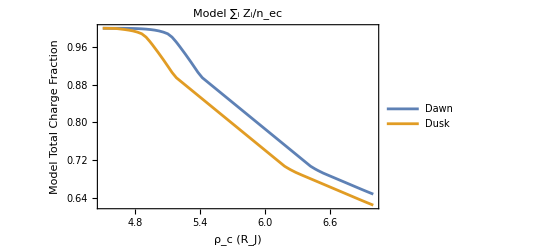

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
SetDirectory["/Users/edne8319/Desktop/from_carl_11-28-22/model_using_emission_tables"]
ρ= Flatten[Import["x_grid_to_plot_60_points.csv","CSV"]];
dawnratio= Flatten[Import["dawn_apo_final_totchmixratio.csv","CSV"]];
duskratio= Flatten[Import["dusk_apo_final_totchmixratio.csv","CSV"]];

dawnratiolist=Table[{ρ[[i]],dawnratio[[i]]},{i,1,Length[ρ],1}];
duskratiolist=Table[{ρ[[i]],duskratio[[i]]},{i,1,Length[ρ],1}];
dawnratiolist = AppendTo[dawnratiolist,{4.5,1.0}];
duskratiolist = AppendTo[duskratiolist,{4.5,1.0}];

dawnratiointerp=Interpolation[dawnratiolist,InterpolationOrder->1];
duskratiointerp=Interpolation[duskratiolist,InterpolationOrder->1];

xpleg=0.8;
ypleg=0.5;

p1=Plot[{dawnratiointerp[x],duskratiointerp[x]},{x,4.5,7},Frame->True,FrameLabel->{"ρ_c (R_J)","Model Total Charge Fraction"},PlotLabel->"Model ∑_i Z_i/n_ec",FrameStyle->Directive[Black,Bold],LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,Bold],PlotLegends->Placed[LineLegend[Automatic,{"Dawn","Dusk"},LabelStyle->Directive[Black,Bold],LegendLayout->{"Row",2}],Scaled[{xpleg,ypleg}]]]
```

```mathematica
dawnratiointerp[4.5]
duskratiointerp[4.5]
dawnratiointerp[4.62]
duskratiointerp[4.62]
```

1.

1.

0.999876

0.999505